# MA255 Tech Lab Assignment #4

## I. Plotting the Gradient Vector Field

First, we define the function:

```mathematica
f[x_,y_]=Cos[x]-2*Sin[y];
p1=VectorPlot[{-Sin[x],-2*Cos[y]},{x,-10,10},{y,-10,10},VectorStyle->Red];
p2=ContourPlot[f[x,y],{x,-10,10},{y,-10,10}];
Show[p2,p1]
```

#### a. Plot the gradient vector field of f and a contour plot of f on the same graph.

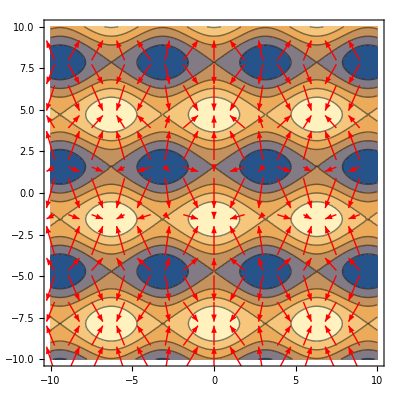

#### b. Based on the graph, explain the relationship between the function and its gradient vector field

The gradient vector field points in the direction of steepest ascent or climb. Dark purple regions classify what might be depressions, while light areas classify areas of higher elevation or positive change. As can be seen by the gradient vector field, the vectors point in the direction of the light areas which confirms the definition of the gradient vector.

## II. Find and Plot the Gradient Vector Field with a 3D Contour Plot

First, we define the 3D function f:

```mathematica
f[x_,y_,z_]=-3*x^2+4*y^2+2*z;
p3=VectorPlot3D[{6*x,8*y,2},{x,-10,10},{y,-10,10},{z,-10,10},VectorStyle->Red];
p4=ContourPlot3D[f[x,y,z],{x,-10,10},{y,-10,10},{z,-10,10},Contours->5];
Show[p3,p4]
```

-Graphics3D-

The graph represents contour surfaces with the gradient vector field overlay to show the direction of steepest change of the contour surfaces.

## III. Graph the Epicycloid and Find the Area Enclosed by the Epicycloid.

Given the parametric equations, graph the epicycloid and find the area enclosed.

#### a. Graph the epicycloid.

```mathematica
VectorPlot[{5*Cos[t]-Cos[5*t],5*Sin[t]-Sin[5*t]},{t,0,Pi}]
```

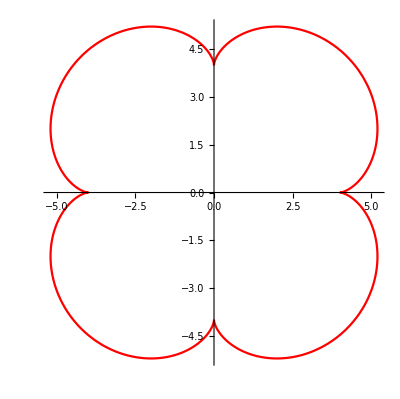

```mathematica
ParametricPlot[{5 Cos[t]-Cos[5 t],5 Sin[t]-Sin[5 t]},{t,0,2*Pi},PlotStyle->Red]
```

#### b. Find the area enclosed by the epicycloid.

We can find the area enclosed by the epicycloid by solving the line integral of the parametric equation x with respect to dy.

```mathematica
x[t_]=5*Cos[t]-Cos[5*t];
y[t_]=5*Sin[t]-Sin[5*t];
∫_0^(2*Pi) x[t]*y'[t]ⅆt
```

30 π

Therefore the area enclosed by the epicycloid is 30π.

## IV. Verify Green’s Theorem

Given the following closed curves, verify Green’s theorem by proving both sides of the equation.

#### a. P(x,y) = x^3 y^4, Q(x,y) = x^5 y^4.

First, we will solve for the left side.

```mathematica
P[x_,y_]=x^3*y^4;
Q[x_,y_]=x^5*y^4;
∫_(-Pi/2)^(Pi/2) (t^3+(-t^5*(Cos[t])^4*(-Sin[t])))ⅆt//N
```

0.0779349

Now, we need to solve for the right hand side to verify Green’s Theorem

```mathematica
∫_(-Pi/2)^(Pi/2) ∫_0^Cos[x] ((5*x^4*y^4)-(4*x^3*y^3))ⅆyⅆx
```

```mathematica
(7578368-932400 π^2+16875 π^4)/253125//N
```

0.0779349

Therefore, this verifies Green’s Theorem. This field is not conservative as can be seen by testing to see if the partial derivative of the P function with respect to y and the partial derivative of the Q function with respect to x equal each other. In this case, the partial derivatives do not equal so it is not conservative.

#### b. P(x,y) = xy^2, Q= x^2 y.

First, we will solve for the left side.

```mathematica
∫_-1^1 t^3 ⅆt
```

0

Now, we need to solve for the right hand side to verify Green’s Theorem.

```mathematica
∫_-1^1 ∫_(x^2)^1 ((2*x*y)-(2*x*y))ⅆyⅆx
```

0

Therefore, this verifies Green’s Theorem. This field is conservative because its partial derivatives are equal to each other. Additionally, we can say that if the line integral of a field is equal to 0, then the field is considered conservative.

## V. Find the Work Done by the Force Field

First, we define the function for our force field:

```mathematica
F[x_,y_,z_]={z,x,y};
```

We are asked to find the work done on a particle as it moves from point (3,0,0) to point (0,π/2,3):

#### a. Along a Straight Line?

In order to find work, we can define the function as the integral of the Force Field function with respect to the r’ function, dotted with the r’ function.
Using the general r equation, r(t) = (1-t)r_0+ tr_1, we can find the r equation.
We get that F(x,y,z)= <-9t,(3π)/2-(3π)/2 t,(3π)/2 t>

```mathematica
∫_0^1 (-9*t+((3*Pi)/2))ⅆt
```

-9/2+(3 π)/2

Therefore, the work done on the particle along a straight line is -9/2+(3 π)/2J.

#### b. The helix given by x = 3cos(t), y = t, and z = 3sin(t)?

Using the same process from before,

```mathematica
∫_0^(Pi/2) (-9*(Sin[t])^2+3*Cos[t]+(3*t*Cos[t]))ⅆt
```

-(3 π)/4

Therefore, the work done on the particle along the helix is -(3 π)/4 .

#### c. Is the force field conservative?

A force field can be determined to be a conservative field if the force field is path independent, meaning the work done in a force field
will be the same no matter what path is taken through the field. This force field is not conservative as the work values for part (a) and part
(b) are not the same meaning the force field is path dependent.